```mathematica
S = {Subscript[α, 1](1-x)-(Subscript[β, 1] x(ν y)^Subscript[γ, 1])/(Subscript[K, 1]+(ν y)^Subscript[γ, 1]),Subscript[α, 2](1-y)-(Subscript[β, 2] y x^Subscript[γ, 2])/(Subscript[K, 2]+x^Subscript[γ, 2]) };
par ={ν->1,Subscript[α, 1]->1, Subscript[α, 2]->1, Subscript[β, 1]->200, Subscript[β, 2]->10, Subscript[γ, 1]->4, Subscript[γ, 2]->4, Subscript[K, 1]->30, Subscript[K, 2]->1};
{Solve[S[[1]]==0,x],Solve[S[[2]]==0,y]}
```

{{{x→(((y ν)^γ_1+K_1) α_1)/((y ν)^γ_1 α_1+K_1 α_1+(y ν)^γ_1 β_1)}},{{y→((x^γ_2+K_2) α_2)/(x^γ_2 α_2+K_2 α_2+x^γ_2 β_2)}}}

```mathematica
Subscript[x, s][y_]=Solve[S[[1]]==0,x][[1,1,2]]/.par
Subscript[y, s][x_]=Solve[S[[2]]==0,y][[1,1,2]]/.par

sol=NSolve[{S[[1]]==0,S[[2]]==0, x>0, y>0}/.par]; pts ={};
For[i=1,i<=Length[sol],i++,
point = {sol[[i,1,2]],sol[[i,2,2]]};
AppendTo[pts,point]]

Print[pts]
```

(30+y^4)/(30+201 y^4)

(1+x^4)/(1+11 x^4)

{{0.994698,0.168157},{0.505774,0.619508},{0.13573,0.996619}}

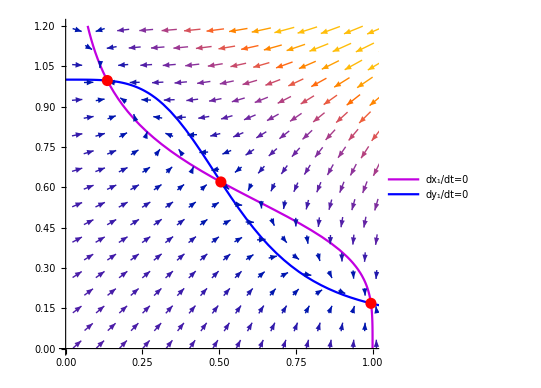

```mathematica
P1=ParametricPlot[{Subscript[x, s][y],y},{y,0,1.2}, PlotStyle->RGBColor[0.76,0,0.88]];
P2=ParametricPlot[{x,Subscript[y, s][x]},{x,0,1.2}, PlotStyle->Blue];
P3=VectorPlot[S/.par,{x,0,1.2},{y,0,1.2}, VectorScaling->Automatic];
P4=ListPlot[pts, PlotStyle->{Red,PointSize[0.02]}];

plot =Show[P1,P2,P3, P4, AspectRatio->0.97];
Legended[plot, LineLegend[{RGBColor[0.76,0,0.88],Blue},{"dx_1/dt=0","dy_1/dt=0"},LabelStyle->{FontSize->10}]]
```

```mathematica
n=1; order=1;
perturbation[ϵ_,δ_]=
  {Normal[Series[D[S[[1]], x]/.par,{x,pts[[n,1]],order},{y,pts[[n,2]],order}]],
Normal[Series[D[S[[1]], y]/.par,{x,pts[[n,1]],order},{y,pts[[n,2]],order}]],
Normal[Series[D[S[[2]], x]/.par,{x,pts[[n,1]],order},{y,pts[[n,2]],order}]],
Normal[Series[D[S[[2]], y]/.par,{x,pts[[n,1]],order},{y,pts[[n,2]],order}]]}/.{x->pts[[n,1]]+ϵ,y->pts[[n,2]]+δ};

perturbation[0,0]
```

{-1.00533,-0.126118,-1.69034,-5.94684}

```mathematica
M = {};
For[i=1,i<=Length[pts],i++,
n=i; order=1;
perturbation[ϵ_,δ_]=
  {Normal[Series[D[S[[1]], x]/.par,{x,pts[[n,1]],order},{y,pts[[n,2]],order}]],
Normal[Series[D[S[[1]], y]/.par,{x,pts[[n,1]],order},{y,pts[[n,2]],order}]],
Normal[Series[D[S[[2]], x]/.par,{x,pts[[n,1]],order},{y,pts[[n,2]],order}]],
Normal[Series[D[S[[2]], y]/.par,{x,pts[[n,1]],order},{y,pts[[n,2]],order}]]}/.{x->pts[[n,1]]+ϵ,y->pts[[n,2]]+δ};
m= {{perturbation[0.00001,0.00001][[1]],perturbation[0,0][[2]]},{perturbation[0,0][[3]],perturbation[0,0][[4]]}};
Print[m//MatrixForm];AppendTo[M,m]]
```

(-1.00533 | -0.126118
-1.69034 | -5.94684)

(-1.97723 | -3.1755
-2.82437 | -1.61418)

(-7.36781 | -3.35837
-0.0996147 | -1.00339)

```mathematica
For[i=1, i<= Length[pts], i++,
	ee=Eigenvalues[M[[i]]];
	WriteString["stdout","Punto ",i,": " ];
	If[ee[[1]]>0 ||ee[[2]]>0,
	WriteString["stdout","Inestable\n"],WriteString["stdout","Estable\n"]]]
```

Punto 1: Estable
Punto 2: Inestable
Punto 3: Estable